```mathematica
Directory[]
```

C:\Users\Prajwal\Documents

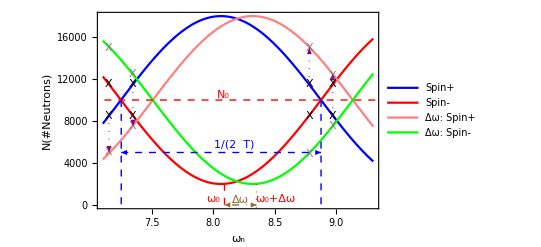

```mathematica
lineStyle={Thin,Red,Dashed};
lineStyle0={Thin,Red,Dotted};
line11=Line[{{7,10000},{9.5,10000}}];
line12=Line[{{8.09,2000},{8.09,-2000}}];
line012=Line[{{8.35,2000},{8.35,-4200}}];
lineStyle2={Thin,Blue,Dashed};
lineStyle3={Thick,Black};
lineStyle4={Thick,Gray};
lineStyle5={Thick,Purple,Dotted};
lineStyle6={Thick,Brown,DotDashed};
line21=Line[{{8.875,10000},{8.875,-2000}}];
line22=Line[{{7.25,10000},{7.25,-2000}}];
pt1[xx_]:=N[10000(1+0.8Cos[3-7(xx*8/29)])];
pt2[xx_]:=N[10000(1-0.8Cos[3-7(xx*8/29)])];
pt3[xx_]:=N[10000(1+0.8Cos[3.5-7(xx*8/29)])];
pt4[xx_]:=N[10000(1-0.8Cos[3.5-7(xx*8/29)])];
exp1=Plot[{pt1[xx],pt2[xx],pt3[xx],pt4[xx]},{xx,7.1,9.3},Frame->True,
Epilog->{
{Directive[lineStyle],line11,line12,Text[Style["N_0",FontSize->Large],{29.3*8/29,10500}],Text[Style["ω_0",FontSize->Large],{8,550}]},
{Directive[lineStyle0],line012,Text[Style["ω_0+Δω",FontSize->Large],{8.5,550}]},
{Directive[lineStyle2],line21,line22,{Arrowheads[{-.02,.02}],Arrow[{{7.25,5000},{8.875,5000}}]},Text[Style["1/(2  T)",FontSize->Large],{29.6*8/29,5750}]},
{Directive[lineStyle3],Text[Style["X",FontSize->Large],{7.15,11500}],Text[Style["X",FontSize->Large],{7.15,8500}],Text[Style["X",FontSize->Large],{7.345,8500}],Text[Style["X",FontSize->Large],{7.345,11500}],(**)Text[Style["X",FontSize->Large],{8.78,8500}],Text[Style["X",FontSize->Large],{8.78,11500}],Text[Style["X",FontSize->Large],{8.97,11500}],Text[Style["X",FontSize->Large],{8.97,8500}]},
{Directive[lineStyle4],Text[Style["X",FontSize->Large],{7.15,11500+3500}],Text[Style["X",FontSize->Large],{7.345,8500+4000}],Text[Style["X",FontSize->Large],{7.15,8500-3500}],Text[Style["X",FontSize->Large],{7.345,11500-4000}],(**)Text[Style["X",FontSize->Large],{8.78,8500-3600}],Text[Style["X",FontSize->Large],{8.97,11500-4000}],Text[Style["X",FontSize->Large],{8.78,11500+3500}],Text[Style["X",FontSize->Large],{8.97,8500+3800}]},
(**){Directive[lineStyle5],{Arrowheads[{0,0.02}],Arrow[{{8.78,11500},{8.78,11500+3500}}]},{Arrowheads[{0,0.02}],Arrow[{{8.97,8500},{8.97,8500+4000}}]},{Arrowheads[{0,0.02}],Arrow[{{7.15,8500},{7.15,8500-3500}}]},{Arrowheads[{0,0.02}],Arrow[{{7.345,11500},{7.345,11500-4000}}]}},
{Directive[lineStyle6],(*For Δω*){Arrowheads[{-.02,0.02}],Arrow[{{8.09,0},{8.35,0}}]},Text[Style["Δω",FontSize->Large],{8.22,500}]},
},
FrameLabel->{"ω_n","N(#Neutrons)"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},PlotLegends->{"Spin+","Spin-","Δω: Spin+","Δω: Spin-"},ImageSize->{1000},
PlotStyle->{Blue,Red,Pink,Green}]
```